# Discrete Power-law fitter

```mathematica
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]]
```

```mathematica
DiscretePowerLawDistributionPDF[α_,xMin_,x_]:=x^-α/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionCDF[α_,xMin_,x_]:=HurwitzZeta[α,x]/HurwitzZeta[α,xMin];
EmpiricalCDF[data_,x_]:= N[1-CDF[EmpiricalDistribution[data],x-1]];
GeneratePowerlawSampleData[α_,xMin_,xMax_,sampleSize_ :1000]:=Block[{dist},
dist = ProbabilityDistribution[DiscretePowerLawDistributionPDF[α,xMin,x],{x,xMin,xMax,1}];

RandomVariate[dist,sampleSize]

];
```

```mathematica
SelectTail[data_,xMin_]:=Select[data,#>=xMin&];
SelectBulk[data_,xMin_]:=Select[data,#<xMin&];
Estimateα[data_,xMin_]:=Block[{n,tail,α},
tail = SelectTail[data,xMin];
n = Length[tail];
α = N[1 + n (∑_(i=1)^n Log[tail[[i]]/(xMin-1/2)])^-1];
<|"Alpha"->α, "xMin"->xMin|>
];
```

```mathematica
KSStatistic[data_,xMin_Integer]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,xMin];
αEstimator = Estimateα[data,xMin]["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,xMin,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,model_Association]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,model["xMin"]];
αEstimator = model["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,model["xMin"],x]],{x,model["xMin"],xMax}];
Max[diff]
];
KSStatistic[data_]:=KSStatistic[data,EstimateαAndXMin[data]];
CalculateLogLikelihood[data_,model_]:=Block[{α, xMin,tail,n},
α = model["Alpha"];
xMin = model["xMin"];
tail = SelectTail[data,xMin];
n = Length[tail];
- n * Log[HurwitzZeta[α,xMin]]-α ∑_(i=1)^n Log[tail[i]]
];
EstimateαAndXMin[data_]:=Block[{minElement,maxElement,xMin},
{minElement,maxElement} = MinMax[data];
xMin = MinimalBy[Table[{x,KSStatistic[data,x]},{x,minElement,maxElement-1}],Last][[1,1]];
Estimateα[data,xMin]
];
GenerateBootstrapReplica[data_,model_]:=Block[{n,bulk, tail,tailProbability,tailReplica,bulkReplica},
n = Length[data];
bulk = SelectBulk[data,model["xMin"]];
tail = SelectTail[data,model["xMin"]];
tailProbability = 1.0 - Length[bulk]/n;
tailReplica = GeneratePowerlawSampleData[model["Alpha"],model["xMin"],Max[data],Floor[n*tailProbability]];
bulkReplica = RandomSample[bulk,n-Floor[n*tailProbability]];
RandomSample[Join[tailReplica, bulkReplica]]
];
GenerateFixedMinBootstrapReplica[model_,xMax_,n_]:=GeneratePowerlawSampleData[model["Alpha"],model["xMin"],xMax,n];
CalculateGOF[data_,replicas_:2000]:=Block[{model,ksOfData,syntheticKsValues,pValue},
model = EstimateαAndXMin[data];
ksOfData = KSStatistic[data,model];
syntheticKsValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[data,model]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->model["Alpha"],"xMin"->model["xMin"],"p-value"->pValue|>
];
CalculateFixedMinGOF[data_,xMin_,replicas_:2000]:=Block[{fixedMinModel,ksOfData,n,syntheticKsValues,pValue},
fixedMinModel = Estimateα[data,xMin];
ksOfData = KSStatistic[data,xMin];
n = Length[SelectTail[data,xMin]];
syntheticKsValues = ProgressTable[KSStatistic[GenerateFixedMinBootstrapReplica[fixedMinModel,Max[data],n]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->fixedMinModel["Alpha"],"xMin"->fixedMinModel["xMin"],"p-value"->pValue|>
];
```

```mathematica
sample = GeneratePowerlawSampleData[2.5,1,100,200]
```

{1,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,2,1,2,1,1,1,1,1,2,4,1,1,2,1,1,1,2,1,2,1,1,1,1,19,1,1,4,1,2,1,1,2,4,1,3,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,4,2,1,1,1,3,1,1,1,1,1,1,1,3,1,1,8,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,5,1,1,1,1,1,1,15,1}

```mathematica
sample = {1,1,2,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,2,1,2,1,1,1,1,1,2,4,1,1,2,1,1,1,2,1,2,1,1,1,1,19,1,1,4,1,2,1,1,2,4,1,3,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,4,2,1,1,1,3,1,1,1,1,1,1,1,3,1,1,8,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,5,1,1,1,1,1,1,15,1};
```

```mathematica
model = <|"Alpha"->2.81,"xMin"->1|>;
```

```mathematica
KSStatistic[sample,<|"Alpha"->2.81,"xMin"->1|>]
```

0.00846968

Fixed x_min

```mathematica
fixedMinModel = Estimateα[sample,4]
```

<|Alpha→2.68281,xMin→4|>

```mathematica
CalculateFixedMinGOF[sample,4,2000]
```

<|Alpha→2.68281,xMin→4,p-value→0.0075|>

```mathematica
KSStatistic[sample,4]
```

0.5

Variable x_min

```mathematica
model = EstimateαAndXMin[sample]
```

<|Alpha→2.5259,xMin→2|>

```mathematica
ksOfSample = KSStatistic[sample,model]
```

0.0659717

```mathematica
ksValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[sample,model]],2000];
```

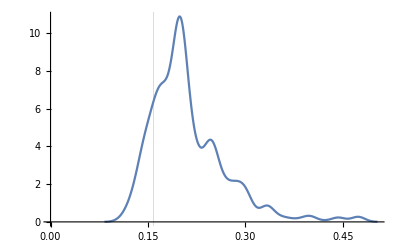

```mathematica
SmoothHistogram[ksValues,GridLines->{{ksOfSample},{}}]
```

```mathematica
N[Count[ksValues,x_ /; x>ksOfSample]/Length[ksValues]]
```

0.853

```mathematica
CalculateGOF[sample]
```

<|Alpha→2.08014,xMin→4,p-value→0.8395|>